```mathematica
Use a Gompertz Distribution as a Lifetime Model
```

```mathematica
r=SurvivalFunction[GompertzMakehamDistribution[λ,ξ],t];

rs=r r;

rp=1-(1-r) (1-r);
```

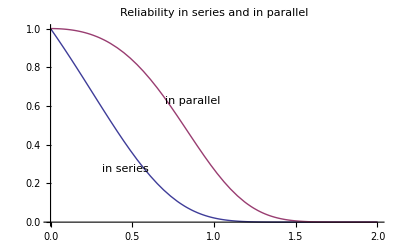

```mathematica
Block[{λ=2,ξ=.3},Framed[Plot[{rs,rp},{t,0,2},PlotStyle->Thick,ImageSize->400,BaseStyle->{FontFamily->"Verdana"},PlotLabel->"Reliability in series and in parallel",Epilog->{Inset[Framed[Style["in parallel",12],Background->LightYellow],{0.7,0.6},{Left,Bottom}],Inset[Framed[Style["in series",12],Background->LightYellow],{0.6,0.3},{Right,Top}]}],RoundingRadius->5,Background->Lighter[Blend[{Yellow,Orange}],0.8]]]
```